# The Bart - Gohberg - Kaashoek - Van Dooren Theorem

### Load NCGB

```mathematica
<<NC`
<<NCAlgebra`
<<NCGBX`
<<NCPolyGroebner`
```

You are using the version of NCAlgebra which is found in:

/Users/mauricio/NC/

You can now use "<< NCAlgebra`" to load NCAlgebra.

## Step 1

```mathematica
Clear[A,B,C,m1,m2,n1,n2,a,b,c,e,f,g]
SetNonCommutative[A,B,C,m1,m2,n1,n2,a,b,c,e,f,g];
```

Clear::wrsym: Symbol C is Protected.

SetNonCommutative::Protected: WARNING: Symbol C is protected. You should seriously consider not setting it as noncommutative.

```mathematica
FAC={A**m1-m1**a-m2**f**c,A**m2-m2**e,B-m1**b-m2**f,-c+C**m1,-g+C**m2,n1**m1-1,n1**m2,n2**m1,n2**m2-1,m1**n1+m2**n2-1};
```

```mathematica
Length[FAC]
```

10

```mathematica
SetKnowns[A,B,C];
SetUnknowns[m1,m2,n1,n2,a,b,c,e,f,g];
```

```mathematica
FACans1=NCProcess[FAC,2, MaxDigest->2, InfiniteDigest->True,VerboseLevel->1,RemoveRedundant->True];
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ m1≪ m2≪ n1≪ n2≪ a≪ b≪ c≪ e≪ f≪ g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 14 polys in the basis, 17 obstructions

> MAJOR Iteration 2, 19 polys in the basis, 34 obstructions

* Removing redundant polynomials

* Basis reduced to 10 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 10 polynomials

* * * * * * * * * * * * * * * *

* * * * * * * * * * * * * * * *

*      NCProcess  Report      *

* * * * * * * * * * * * * * * *

> Current order:

A<B<C≪ m1≪ m2≪ n1≪ n2≪ a≪ b≪ c≪ e≪ f≪ g

> The following variables have been solved for:

1. | c→C**m1
2. | g→C**m2
3. | e→n2**A**m2
4. | f→n2**B-n2**m1**b

> The following variables have not been solved for:

,,aAbBCm1m2n1n2

> The following relations involve 2 unknowns:

+ in unknowns {m1,n1}:

1. | n1**m1→1

+ in unknowns {m1,n2}:

1. | n2**m1→0

+ in unknowns {m2,n1}:

1. | n1**m2→0
2. | n1**A**m2→0

+ in unknowns {m2,n2}:

1. | n2**m2→1

> The following relations involve more than 2 unknowns:

+ in unknowns {m1,m2,n1,n2}:

1. | m2**n2→1-m1**n1

```mathematica
FACans1
```

<|Solved→{c→C**m1,g→C**m2,e→n2**A**m2,f→n2**B-n2**m1**b},0→<||>,1→<||>,2→<|{m1,n1}→{n1**m1→1},{m1,n2}→{n2**m1→0},{m2,n1}→{n1**m2→0,n1**A**m2→0},{m2,n2}→{n2**m2→1}|>,∞→<|{m1,m2,n1,n2}→{m2**n2→1-m1**n1}|>|>

## Step 2

```mathematica
Clear[P1]
```

```mathematica
SetNonCommutative[P1];
```

```mathematica
SetKnowns[P1,A,B,C];
SetUnknowns[{m1,m2,n1,n2},{a,b,c,e,f,g}];
```

```mathematica
discovered={m1**n1-P1,n1**m1-1,n2**m2-1,m2**n2-1+m1**n1};
(*relations=Union[FACans1[[2]],FACans1[[3]],discovered];*)
```

```mathematica
discovered={m1**n1-P1}
relations=Union[FAC,discovered]
```

{-P1+m1**n1}

{-c+C**m1,-g+C**m2,-P1+m1**n1,A**m2-m2**e,B-m1**b-m2**f,-1+m1**n1+m2**n2,-1+n1**m1,n1**m2,n2**m1,-1+n2**m2,A**m1-m1**a-m2**f**c}

```mathematica
Length[relations]
```

11

```mathematica
FACans2=NCProcess[relations,3,VerboseLevel->1,RemoveRedundant->True,CleanUpBasis->True];
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

> MAJOR Iteration 3, 28 polys in the basis, 48 obstructions

* Cleaning up...

* Removing redundant polynomials

* Basis reduced to 11 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 11 polynomials

* * * * * * * * * * * * * * * *

* * * * * * * * * * * * * * * *

*      NCProcess  Report      *

* * * * * * * * * * * * * * * *

> Current order:

P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

> The following variables have been solved for:

1. | c→C**m1
2. | g→C**m2
3. | e→n2**A**m2
4. | a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1

> The following variables have not been solved for:

,,AbBCfm1m2n1n2P1

> The following relations do not involve any unknowns:

1. | P1**A**A**P1→P1**A**P1**A

> The following relations involve 2 unknowns:

+ in unknowns {m1,n1}:

1. | m1**n1→P1
2. | n1**m1→1

+ in unknowns {m1,n2}:

1. | n2**m1→0

+ in unknowns {m2,n1}:

1. | n1**m2→0

+ in unknowns {m2,n2}:

1. | n2**m2→1

> The following relations involve more than 2 unknowns:

+ in unknowns {m1,m2,n1,n2}:

1. | m2**n2→1-m1**n1

```mathematica
FACans2
```

<|Solved→{c→C**m1,g→C**m2,e→n2**A**m2,a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1},0→<|{}→{P1**A**A**P1→P1**A**P1**A}|>,1→<||>,2→<|{m1,n1}→{m1**n1→P1,n1**m1→1},{m1,n2}→{n2**m1→0},{m2,n1}→{n1**m2→0},{m2,n2}→{n2**m2→1}|>,∞→<|{m1,m2,n1,n2}→{m2**n2→1-m1**n1}|>|>

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Options:

> VerboseLevel         -> 4

> SortBasis            -> False

> SimplifyObstructions -> True

> SortObstructions     -> False

> PrintObstructions    -> False

> PrintBasis           -> False

> PrintSPolynomials    -> False

* Monomial order: P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

> G(0) = {-c,C.m1}
{-g,C.m2}
{m1.n1,-P1}
{-m2.e,A.m2}
{-m2.f,-m1.b,B}
{m2.n2,m1.n1,-1}
{n1.m1,-1}
{n1.m2}
{n2.m1}
{n2.m2,-1}
{-m2.f.c,-m1.a,A.m1}

* Reduce and normalize initial set

> Initial set could not be reduced

> G(0) = {c,-C.m1}
{g,-C.m2}
{m1.n1,-P1}
{m2.e,-A.m2}
{m2.f,m1.b,-B}
{m2.n2,m1.n1,-1}
{n1.m1,-1}
{n1.m2}
{n2.m1}
{n2.m2,-1}
{m1.b.C.m1,-m1.a,-B.C.m1,A.m1}

* Initializing G tree

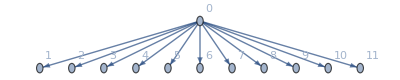
> GTree = -Graphics-

* Extracting leading monomials

> TG(0) = {{c},{g},{m1.n1},{m2.e},{m2.f},{m2.n2},{n1.m1},{n1.m2},{n2.m1},{n2.m2},{m1.b.C.m1}}

* Computing initial set of obstructions

- Minor Iteration 1, 11 polys in the basis, 16 obstructions

* Selecting obstruction OBS(3,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

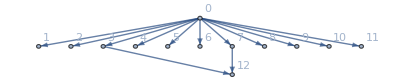
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 2, 12 polys in the basis, 16 obstructions

* Selecting obstruction OBS(3,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

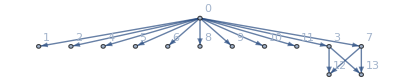
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 3, 13 polys in the basis, 18 obstructions

* Selecting obstruction OBS(3,8)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

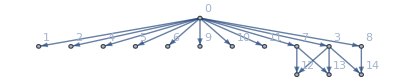
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 4, 14 polys in the basis, 21 obstructions

* Selecting obstruction OBS(4,8)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

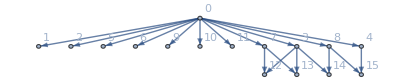
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 5, 15 polys in the basis, 24 obstructions

* Selecting obstruction OBS(5,8)

* Building S-Polynomial

* Reducing S-Polynomial

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

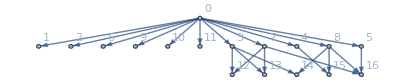
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

* Acyclic? = True

* Simplify current set of obstructions

* Removing obstructions ({3, 11}) from set of obstructions

* Removing obstructions ({7, 11}) from set of obstructions

* Removing obstructions ({9, 11}) from set of obstructions

* Removing obstructions ({11, 11}) from set of obstructions

* Removing obstructions ({11, 13}) from set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 11

* Node contains 0

> Poly 11 does not reduce to zero; remainder added to base

* S-Polynomial added to current basis

* Added node to GTree

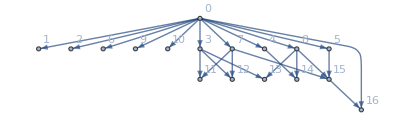
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Replaced at GTree

* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

* Acyclic? = True

- Minor Iteration 6, 16 polys in the basis, 21 obstructions

* Selecting obstruction OBS(6,8)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 7, 16 polys in the basis, 20 obstructions

* Selecting obstruction OBS(3,9)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

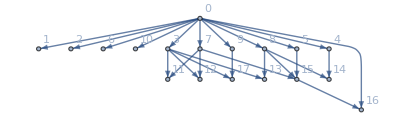
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 8, 17 polys in the basis, 22 obstructions

* Selecting obstruction OBS(6,9)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 9, 17 polys in the basis, 21 obstructions

* Selecting obstruction OBS(4,10)

* Building S-Polynomial

* Reducing S-Polynomial

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

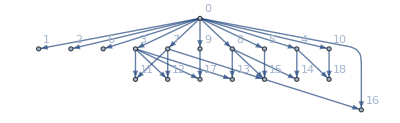
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 4

* Node contains 0

> Poly 4 does not reduce to zero; remainder added to base

* S-Polynomial added to current basis

* Added node to GTree

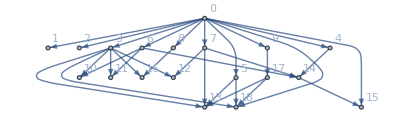
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Replaced at GTree

* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

* Acyclic? = True

- Minor Iteration 10, 18 polys in the basis, 22 obstructions

* Selecting obstruction OBS(4,9)

* Building S-Polynomial

* Reducing S-Polynomial

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

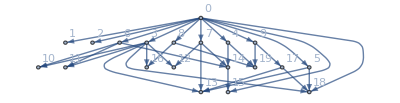
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 4

* Node contains 0

* Removed from GTree

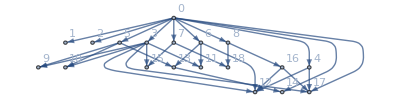
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

* Acyclic? = True

> Poly 4 reduced to zero; removing from base

- Minor Iteration 11, 18 polys in the basis, 18 obstructions

* Selecting obstruction OBS(4,8)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 12, 18 polys in the basis, 17 obstructions

* Selecting obstruction OBS(4,8)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 13, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

* Selecting obstruction OBS(3,9)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

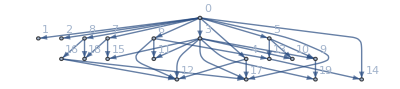
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 14, 19 polys in the basis, 21 obstructions

* Selecting obstruction OBS(3,10)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 15, 19 polys in the basis, 20 obstructions

* Selecting obstruction OBS(9,10)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 16, 19 polys in the basis, 19 obstructions

* Selecting obstruction OBS(4,11)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 17, 19 polys in the basis, 18 obstructions

* Selecting obstruction OBS(9,11)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 18, 19 polys in the basis, 17 obstructions

* Selecting obstruction OBS(3,12)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 19, 19 polys in the basis, 16 obstructions

* Selecting obstruction OBS(4,12)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

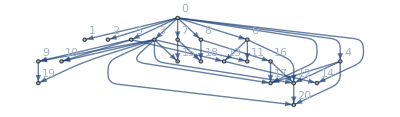
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 20, 20 polys in the basis, 20 obstructions

* Selecting obstruction OBS(5,14)

* Building S-Polynomial

* Reducing S-Polynomial

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

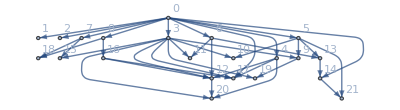
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 14

* Node contains 0

> Poly 14 does not reduce to zero; remainder added to base

* S-Polynomial added to current basis

* Added node to GTree

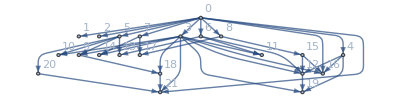
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Replaced at GTree

* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

* Acyclic? = True

- Minor Iteration 21, 21 polys in the basis, 22 obstructions

* Selecting obstruction OBS(4,14)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 22, 21 polys in the basis, 21 obstructions

* Selecting obstruction OBS(10,14)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 23, 21 polys in the basis, 20 obstructions

* Selecting obstruction OBS(11,14)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 24, 21 polys in the basis, 19 obstructions

* Selecting obstruction OBS(4,16)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

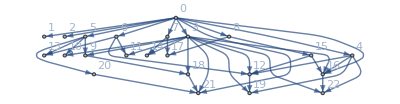
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 25, 22 polys in the basis, 28 obstructions

* Selecting obstruction OBS(9,16)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 26, 22 polys in the basis, 27 obstructions

* Selecting obstruction OBS(14,16)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 27, 22 polys in the basis, 26 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

* Selecting obstruction OBS(9,18)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 28, 22 polys in the basis, 25 obstructions

* Selecting obstruction OBS(10,18)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 29, 22 polys in the basis, 24 obstructions

* Selecting obstruction OBS(11,18)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 30, 22 polys in the basis, 23 obstructions

* Selecting obstruction OBS(14,18)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 31, 22 polys in the basis, 22 obstructions

* Selecting obstruction OBS(16,18)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 32, 22 polys in the basis, 21 obstructions

* Selecting obstruction OBS(18,18)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 33, 22 polys in the basis, 20 obstructions

* Selecting obstruction OBS(3,19)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 34, 22 polys in the basis, 19 obstructions

* Selecting obstruction OBS(10,19)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 35, 22 polys in the basis, 18 obstructions

* Selecting obstruction OBS(11,19)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 36, 22 polys in the basis, 17 obstructions

* Selecting obstruction OBS(16,19)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

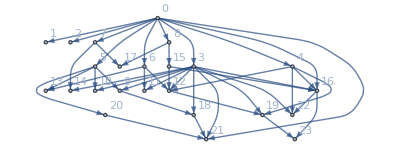
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 37, 23 polys in the basis, 18 obstructions

* Selecting obstruction OBS(18,19)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 38, 23 polys in the basis, 17 obstructions

* Selecting obstruction OBS(3,21)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

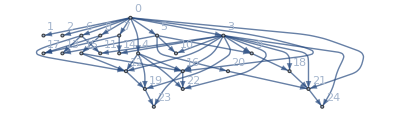
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 39, 24 polys in the basis, 28 obstructions

* Selecting obstruction OBS(9,21)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 40, 24 polys in the basis, 27 obstructions

* Selecting obstruction OBS(14,21)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

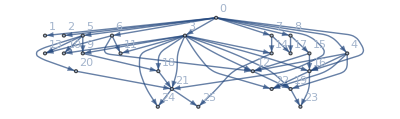
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 41, 25 polys in the basis, 28 obstructions

* Selecting obstruction OBS(18,21)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 42, 25 polys in the basis, 27 obstructions

* Selecting obstruction OBS(19,21)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 43, 25 polys in the basis, 26 obstructions

* Selecting obstruction OBS(9,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 44, 25 polys in the basis, 25 obstructions

* Selecting obstruction OBS(10,22)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 45, 25 polys in the basis, 24 obstructions

* Selecting obstruction OBS(11,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 46, 25 polys in the basis, 23 obstructions

* Selecting obstruction OBS(14,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 47, 25 polys in the basis, 22 obstructions

* Selecting obstruction OBS(16,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

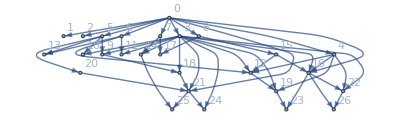
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 48, 26 polys in the basis, 28 obstructions

* Selecting obstruction OBS(18,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 49, 26 polys in the basis, 27 obstructions

* Selecting obstruction OBS(18,22)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 50, 26 polys in the basis, 26 obstructions

* Selecting obstruction OBS(19,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

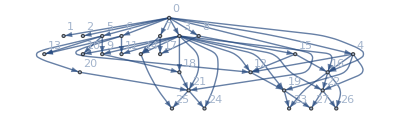
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 51, 27 polys in the basis, 34 obstructions

* Selecting obstruction OBS(21,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 52, 27 polys in the basis, 33 obstructions

* Selecting obstruction OBS(22,22)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

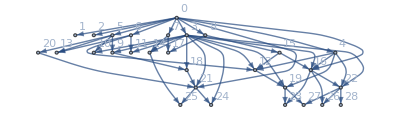
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 53, 28 polys in the basis, 48 obstructions

> MAJOR Iteration 3, 28 polys in the basis, 48 obstructions

* Cleaning up...

* Cleaning up 1th basis entry

* Cleaning up 2th basis entry

* Cleaning up 3th basis entry

* Cleaning up 4th basis entry

* Cleaning up 5th basis entry

* Cleaning up 6th basis entry

* Cleaning up 7th basis entry

* Cleaning up 8th basis entry

* Cleaning up 9th basis entry

* Cleaning up 10th basis entry

* Cleaning up 11th basis entry

* Cleaning up 12th basis entry

* Cleaning up 13th basis entry

* Cleaning up 14th basis entry

* Cleaning up 15th basis entry

* Cleaning up 16th basis entry

* Cleaning up 17th basis entry

* Cleaning up 18th basis entry

* Cleaning up 19th basis entry

* Cleaning up 20th basis entry

* Cleaning up 21th basis entry

* Cleaning up 22th basis entry

* Cleaning up 23th basis entry

* Cleaning up 24th basis entry

* Cleaning up 25th basis entry

* Cleaning up 26th basis entry

* Cleaning up 27th basis entry

* Cleaning up 28th basis entry

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 28 polynomials

* * * * * * * * * * * * * * * *

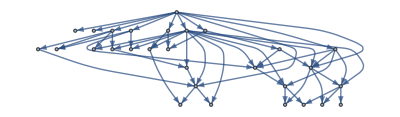
{{c→C**m1,g→C**m2,m1**n1→P1,m2**n2→1-m1**n1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**P1→n1,P1**m1→m1,P1**m2→0,n1**A**m2→0,b→n1**B,n2**P1→0,e→n2**A**m2,P1**A**m2→0,f→n2**B,P1**P1→P1,n1**A**P1→n1**A,a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,P1**A**P1→P1**A,n1**A**A**m2→0,P1**B**C**P1→-A**P1+B**C**P1+P1**A**P1,n2**B**C**m1→n2**A**m1-n2**P1**A**m1,P1**A**A**m2→0,n1**A**A**P1→n1**A**P1**A,P1**A**A**P1→P1**A**P1**A},-Graphics-}

```mathematica
{gg1,graph}=NCMakeGB[relations,3,VerboseLevel->4,ReturnGraph->True,RemoveRedundant->False,CleanUpBasis->True]
```

```mathematica
Pick[VertexList[graph],VertexInDegree[graph],_?(#≤1&)]
```

{0,1,2,3,4,5,6,7,8,15,20,28}

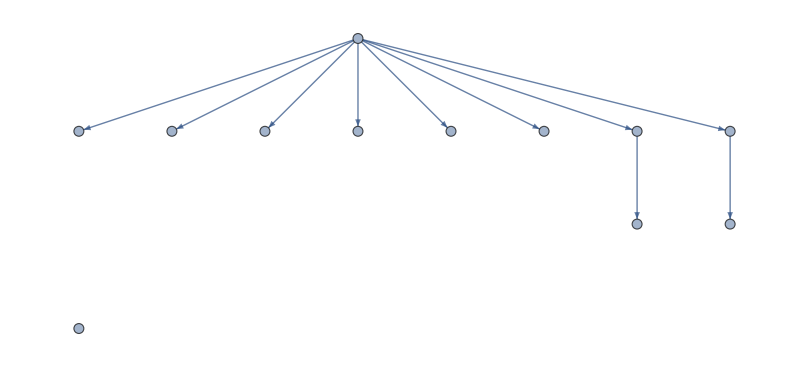

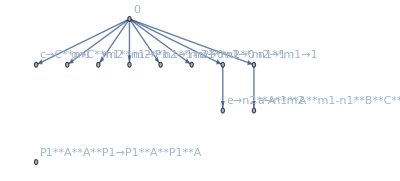

```mathematica
Subgraph[graph,Pick[VertexList[graph],VertexInDegree[graph],_?(#≤1&)]]
VertexReplace[%,Thread[Range[Length[gg1]]->gg1]];
Graph[%,VertexLabels->"Name"]
```

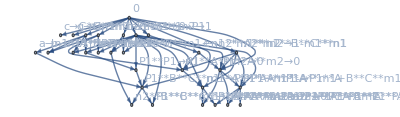

```mathematica
VertexReplace[graph,Thread[Range[Length[gg1]]->gg1]];
Graph[%,VertexLabels->"Name"]
```

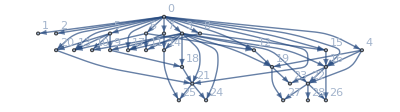

```mathematica
Graph[graph,VertexLabels->"Name"]
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ P1≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

* Removing redundant polynomials

* Basis reduced to 15 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 15 polynomials

* * * * * * * * * * * * * * * *

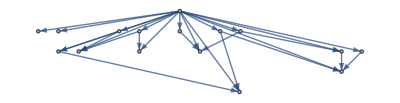
{{P1**A**m2→0,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,m1**n1→P1,m2**n2→1-P1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**A**m2→0,a→n1**P1**A**m1,b→n1**B,c→C**m1,e→n2**A**m2,f→n2**B,g→C**m2},-Graphics-}

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ P1≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 22 polys in the basis, 35 obstructions

> MAJOR Iteration 2, 31 polys in the basis, 88 obstructions

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 31 polynomials

* * * * * * * * * * * * * * * *

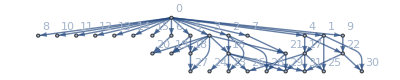
{{P1**P1→P1,P1**A**P1→P1**A,P1**A**A**P1→P1**A**A,P1**B**C**P1→-A**P1+P1**A+B**C**P1,P1**B**C**B**C**P1→A**A**P1-P1**A**A-A**B**C**P1-B**C**A**P1+B**C**B**C**P1+P1**A**B**C**P1+P1**B**C**A**P1,P1**m1→m1,P1**m2→0,n1**P1→n1,n2**P1→0,P1**A**m2→0,n1**A**P1→n1**A,P1**A**A**m2→0,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,n1**A**A**P1→n1**A**A,n2**B**C**P1→n2**A**P1,P1**B**C**B**C**m1→A**A**m1-A**B**C**m1-B**C**A**m1-P1**A**A**m1+B**C**B**C**m1+P1**A**B**C**m1+P1**B**C**A**m1,m1**n1→P1,m2**n2→1-P1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**A**m2→0,n1**A**A**m2→0,n2**B**C**m1→n2**A**m1,a→n1**A**m1,b→n1**B,c→C**m1,e→n2**A**m2,f→n2**B,g→C**m2},-Graphics-}

{}

```mathematica
{gg2,graph}=NCMakeGB[relations,2,VerboseLevel->1,ReturnGraph->True,RemoveRedundant->True]
{gg3,graph}=NCMakeGB[gg2,2,VerboseLevel->1,ReturnGraph->True,RemoveRedundant->False]
Complement[gg1,gg3]
```